```mathematica
data=Rescale[Import["/Users/michi/Documents/LeanXcam/source/LeanXsugus/Extras/Klassifikation/normalized/"<>"color-"<>#<>".txt","Table"]&/@{"green","yellow","orange","red"},{0,255}]
```

{{{88/255,116/255,61/255},{71/255,104/255,53/255},{77/255,109/255,52/255},{22/85,92/255,8/51},{58/255,98/255,14/85},{149/255,11/15,22/51},{5/17,37/85,53/255},«986»,{29/85,128/255,4/15},{109/255,143/255,27/85},{76/255,36/85,56/255},{91/255,127/255,14/51},{5/17,104/255,19/85},{13/85,4/15,31/255},{8/51,67/255,29/255}},«1»,«1»,{{«1»},«998»,{«1»}}}

```mathematica
RGBToHSV[l:{r_,g_,b_}]:=
Block[
{min=Min[l],max=Max[l]},
{Mod[Piecewise[{{0,max==min},{(g-b)/(max-min)/6,max==r},{(b-r)/(max-min)/6+1/3,max==g},{(r-g)/(max-min)/6+2/3,max==b}}],1],Piecewise[{{0,max==0}},(max-min)/max],max}
]
```

```mathematica
Table[
ContourPlot3D[({x,y,z}.{a,b,c}/(a^2+b^2+c^2)-1/.i⟦1⟧)==0,{x,0,1},{y,0,1},{z,0,1},Mesh->10,MeshFunctions->(#3&),MeshShading->{Directive[i⟦2⟧,Opacity[1/2]],Directive[i⟦3⟧,Opacity[1/2]]},MeshStyle->None,BoundaryStyle->None,Lighting->{{"Ambient",White}},AxesLabel->{"Red","Green","Blue"}],
{i,{
{{a->-0.0000681308,b->0.0000651819,c->-1.25607*10^-6},Green,Yellow},
{{a->-0.0000599022,b->0.0000925811,c->-0.0000473431},Yellow,Orange},
{{a->-6.77692*10^-8,b->6.07596*10^-7,c->-8.26222*10^-7},Orange,Red}
}}
]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
ListPointPlot3D[data,BoxRatios->Automatic,PlotRange->{{0,1},{0,1},{0,1}},PlotStyle->{Green,Yellow,Orange,Red},AxesLabel->{"R","G","B"}]
```

-Graphics3D-

```mathematica
Show[%,%%⟦1⟧]
```

-Graphics3D-

```mathematica
Show[ListPointPlot3D[Flatten[Table[{x,y,z},{x,0,1,1/10},{y,0,1,1/10},{z,0,1,1/10}],2],BoxRatios->Automatic,ColorFunction->RGBColor],ListPointPlot3D[data,BoxRatios->Automatic,PlotRange->{{0,1},{0,1},{0,1}},PlotStyle->{Green,Yellow,Orange,Red},AxesLabel->{"R","G","B"}]]
```

-Graphics3D-

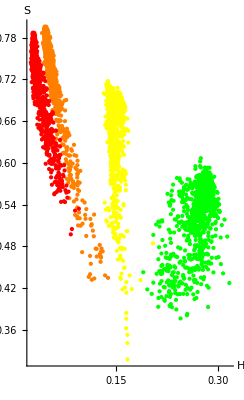

```mathematica
ListPlot[Map[RGBToHSV,data,{2}]⟦All,All,{1,2}⟧,AspectRatio->Automatic,PlotStyle->{Green,Yellow,Orange,Red},AxesLabel->{"H","S"}]
```

```mathematica
ListPointPlot3D[Map[RGBToHSV,data,{2}],BoxRatios->Automatic,PlotStyle->{Green,Yellow,Orange,Red},AxesLabel->{"H","S","V"}]
```

-Graphics3D-

```mathematica
Clear[log];log[x_,a_:1]:=(ⅇ^(a x)-1)/(ⅇ^(a x)+1)
```

```mathematica
dist[{x_,y_,z_},{a_,b_,c_}]:=(({x,y,z}.{a,b,c})/(a^2+b^2+c^2)-1)
```

FindMaximum::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

{4000.,{a→-0.0000599022,b→0.0000925811,c→-0.0000473431}}

2000

2000

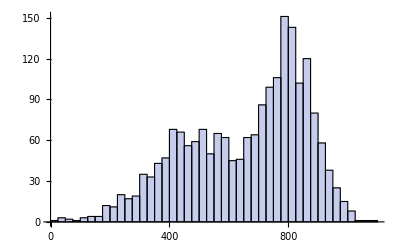

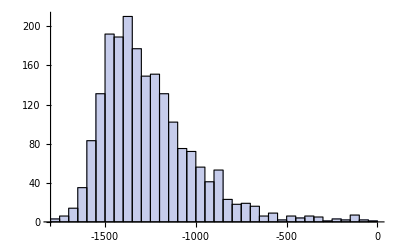

```mathematica
Needs["Histograms`"]
data1=data⟦1⟧;
data2=data⟦2⟧;
data1=data⟦3⟧;
data2=data⟦4⟧;
data1=Join[data⟦1⟧,data⟦2⟧];
data2=Join[data⟦3⟧,data⟦4⟧];
sol=FindMaximum[
{Total[log[dist[#,{a,b,c}]]&/@data1]-Total[log[dist[#,{a,b,c}]]&/@data2]},
{{a,1},{b,1},{c,1}}
]
Count[dist[#,{a,b,c}/.sol⟦2⟧]&/@data1,_?Positive]
Count[dist[#,{a,b,c}/.sol⟦2⟧]&/@data2,_?Negative]
dist[#,{a,b,c}/.sol⟦2⟧]&/@data1//Histogram
dist[#,{a,b,c}/.sol⟦2⟧]&/@data2//Histogram
```